```mathematica
Asym[n_]:=Module[{u,a,x1,x2,y1,y2,r,θ,x,y},u=RandomVariate[UniformDistribution[],n];
a=4/π;
x1=a √u;
x1=a-x1;
y1=RandomVariate[UniformDistribution[Transpose[{x1/a-1,1-x1/a}]]];
u=RandomVariate[UniformDistribution[],n];
r=√u;
θ=RandomVariate[UniformDistribution[{π/2,(3 π)/2}],n];
x2=r Cos[θ];
y2=r Sin[θ];
x=Flatten[{x1,x2}];
y=Flatten[{y1,y2}];
Transpose[{x,y}]]
Sqr[n_]:=Module[{x,y},
x=RandomVariate[UniformDistribution[{-0.5,0.5}],2n];
y=RandomVariate[UniformDistribution[{-0.5,0.5}],2n];
Transpose[{x,y}]]
Crc[n_]:=Module[{u,r,θ,x,y},
u=RandomVariate[UniformDistribution[],2n];
r=√u;
θ=RandomVariate[UniformDistribution[{0,2π}],2n];
x=r Cos[θ];
y=r Sin[θ];
Transpose[{x,y}]]
b[X_]:=Module[{n,Z},
n=Length[X];
Z=Standardize[X];
Max[Table[Abs[1/n∑_(i=1)^n ({Cos[(2k π)/100],Sin[(2k π)/100]}.Z[[i]])^3],{k,100}]]]
bp[X_,M_]:=Module[{n,bn,XM,bnM},
n=Length[X];
bn=b[X];
XM=Table[RandomChoice[{-1,1},n]X,{m,M}];
bnM=Table[b[XM[[m]]],{m,M}];
N[(∑_(m=1)^M Boole[bnM[[m]]≥bn])/M]]
S2[X_,K_]:=Module[{n,PX,s,c,ν},
n=Length[X];
PX=Table[Normalize[X[[i]]],{i,n}];
s=Table[∑_(i=1)^n Sin[k ArcSin[PX[[i]][[2]]]],{k,K}];
c=Table[∑_(i=1)^n Cos[k ArcCos[PX[[i]][[1]]]],{k,K}];
ν=Flatten[Transpose[{s,c}]];
Norm[ν]^2]
S2p[X_,K_,M_]:=Module[{n,S,XM,SM},
n=Length[X];
S=S2[X,K];
XM=Table[Table[Norm[X[[i]]],{i,n}]Table[{Cos[θ],Sin[θ]},{θ,RandomVariate[UniformDistribution[{0,2π}],n]}],{m,M}];
SM=Table[S2[XM[[m]],K],{m,M}];
N[(∑_(m=1)^M Boole[SM[[m]]≥S])/M]]
```

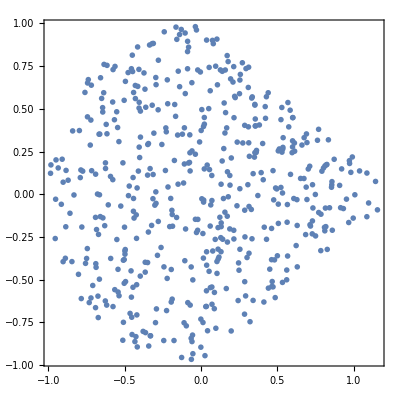
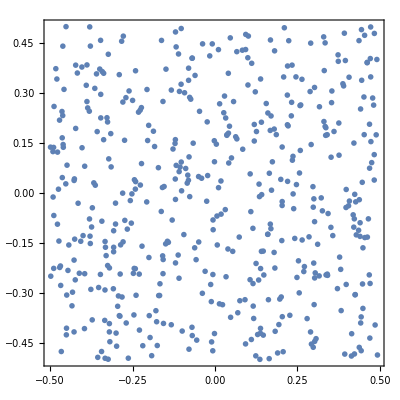
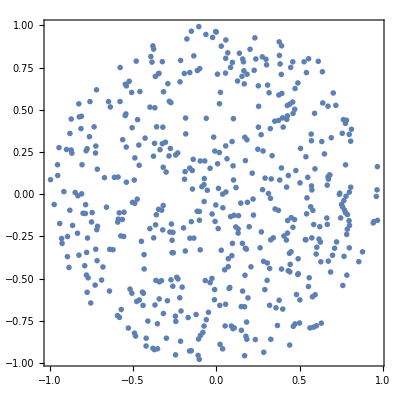

```mathematica
Table[ListPlot[X,Frame->True,Axes->False,AspectRatio->1,PlotStyle->PointSize[Medium],PlotMarkers->"OpenMarkers"],{X,{Asym[250],Sqr[250],Crc[250]}}]
```

```mathematica
X=Table[Asym[350],100];
p=Parallelize[Table[S2p[X[[i]],5,1000],{i,100}]]
```

{0.,0.,0.,0.001,0.006,0.,0.002,0.,0.085,0.006,0.009,0.,0.,0.092,0.011,0.001,0.018,0.016,0.002,0.01,0.,0.005,0.014,0.245,0.007,0.,0.032,0.074,0.,0.001,0.006,0.119,0.005,0.,0.006,0.001,0.001,0.05,0.,0.629,0.006,0.002,0.009,0.024,0.,0.,0.087,0.034,0.024,0.103,0.001,0.,0.022,0.001,0.002,0.002,0.066,0.009,0.,0.04,0.149,0.001,0.051,0.006,0.,0.188,0.004,0.001,0.,0.125,0.005,0.,0.011,0.028,0.029,0.005,0.002,0.089,0.041,0.017,0.006,0.01,0.,0.07,0.039,0.002,0.002,0.014,0.,0.,0.081,0.001,0.011,0.003,0.,0.004,0.005,0.,0.,0.042}

```mathematica
∑_(k=1)^100 Boole[p[[k]]≥0.05]
∑_(k=1)^100 Boole[p[[k]]≥0.1]
```

17

7